```mathematica
$MachineName
```

snowy01

```mathematica
Directory[]
```

/home/ashmat

```mathematica
SetDirectory["/home/ashmat/Projects/myxo-project/"];
```

```mathematica
reloadPackage[]:=(Quiet[Unprotect["BiharmonicSolver`*"];
ClearAll["BiharmonicSolver`*"];
ClearAll["BiharmonicSolver`Private`*"];
Remove["BiharmonicSolver`*"];
Remove["BiharmonicSolver`Private`*"];];
Get["BiharmonicSolverFourier.wl"])
```

```mathematica
reloadPackage[]
```

```mathematica
params={S0->1,l->1,lM->7.0/3,lm->0.7/3};
W=10;
S[r_]:=S0 f[r/l]
f[x_]:=x √((0.34+0.07 x^2)/(1+0.41 x^2+0.07 x^4))
θ[ϕ_]:=ϕ/2
Q[x_,y_]:={{S[r] Cos[2θ[ϕ]],S[r] Sin[2θ[ϕ]]},{S[r] Sin[2θ[ϕ]],-S[r] Cos[2θ[ϕ]]}}/.{r->√(x^2+y^2),ϕ->ArcTan[x,y]}
```

```mathematica
A[x_,y_]:=1/2(IdentityMatrix[2]+Q[x,y])
Σ[x_,y_]:=1/2 IdentityMatrix[2](lM^2+lm^2)+1/2 Q[x,y](lM^2-lm^2)
G[x1_,y1_,x2_,y2_]:=1/2(A[x1,y1]PDF[MultinormalDistribution[{x1,y1},Σ[x1,y1]],{x2,y2}]
+A[x2,y2]PDF[MultinormalDistribution[{x2,y2},Σ[x2,y2]],{x1,y1}])
```

```mathematica
cfG=Compile[{x1,y1,x2,y2},G[x1,y1,x2,y2]/.params//Evaluate];
```

```mathematica
(*Run solver*)
```

```mathematica
cfG[1.,0.,0.5,0.3]
```

{{0.042453,0.00240709},{0.00240709,0.0177454}}

```mathematica
G[x1_,y1_,x2_,y2_]=IdentityMatrix[2]Exp[-{x1-x2,y1-y2}.{x1-x2,y1-y2}/2];
cfG=Compile[{x1,y1,x2,y2},G[x1,y1,x2,y2]//Evaluate];
```

```mathematica
LaunchKernels[2$ProcessorCount];(*start parallel kernels if not already running*)
```

```mathematica
sols=Association[];
```

```mathematica
sols[{128,32.0}]=solveBiharmonicFourier[cfG,128,32.0,"Method"->"Compiled"];
```

===============================================

Biharmonic Fourier Solver

===============================================

Grid size: 128^4 = 268435456 points

Domain: [-32., 32.]^2 x [-32., 32.]^2

Method: Compiled

-----------------------------------------------

[Step 1/4] Evaluating G_{ij} on 4D grid (parallelized)...

Extracting G components...

Done. (41.59 s)

Memory for G components: ~8192. MB

[Step 2/4] Computing 4D FFT of G components...

Done. (16.42 s)

[Step 3/4] Pointwise division in Fourier space...

Regularization eps = 3.46×10^-13

Done. (30.93 s)

[Step 4/4] Computing inverse 4D FFT...

Done. (4.09 s)

-----------------------------------------------

Max |f| = 2.152×10^-1

Solution complete.

===============================================

```mathematica
sols[{32,8.0}]=solveBiharmonicFourier[cfG,32,8.0,"Method"->"Compiled"];
sols[{64,16.0}]=solveBiharmonicFourier[cfG,64,16.0,"Method"->"Compiled"];
sols[{128,32.0}]=solveBiharmonicFourier[cfG,128,32.0,"Method"->"Compiled"];
```

═══════════════════════════════════════════════

Biharmonic Fourier Solver

═══════════════════════════════════════════════

Grid size: 32^4 = 1048576 points

Domain: [-8., 8.]^2 x [-8., 8.]^2

Method: Compiled

───────────────────────────────────────────────

[Step 1/4] Evaluating G_{ij} on 4D grid (parallelized)...

Extracting G components...

Done. (0.4 s)

Memory for G components: ~32. MB

[Step 2/4] Computing 4D FFT of G components (4 parallel FFTs)...

Done. (0.18 s)

[Step 3/4] Pointwise division in Fourier space...

Regularization eps = 2.27×10^-8

Done. (0.21 s)

[Step 4/4] Computing inverse 4D FFT...

Done. (0.01 s)

───────────────────────────────────────────────

Max |f| = 1.415

Solution complete.

═══════════════════════════════════════════════

═══════════════════════════════════════════════

Biharmonic Fourier Solver

═══════════════════════════════════════════════

Grid size: 64^4 = 16777216 points

Domain: [-16., 16.]^2 x [-16., 16.]^2

Method: Compiled

───────────────────────────────────────────────

[Step 1/4] Evaluating G_{ij} on 4D grid (parallelized)...

Extracting G components...

Done. (1.79 s)

Memory for G components: ~512. MB

[Step 2/4] Computing 4D FFT of G components (4 parallel FFTs)...

Done. (1.7 s)

[Step 3/4] Pointwise division in Fourier space...

Regularization eps = 8.86×10^-11

Done. (1.97 s)

[Step 4/4] Computing inverse 4D FFT...

Done. (0.17 s)

───────────────────────────────────────────────

Max |f| = 2.099

Solution complete.

═══════════════════════════════════════════════

═══════════════════════════════════════════════

Biharmonic Fourier Solver

═══════════════════════════════════════════════

Grid size: 128^4 = 268435456 points

Domain: [-32., 32.]^2 x [-32., 32.]^2

Method: Compiled

───────────────────────────────────────────────

[Step 1/4] Evaluating G_{ij} on 4D grid (parallelized)...

Extracting G components...

Done. (25.04 s)

Memory for G components: ~8192. MB

[Step 2/4] Computing 4D FFT of G components (4 parallel FFTs)...

Done. (25.06 s)

[Step 3/4] Pointwise division in Fourier space...

Regularization eps = 3.46×10^-13

Done. (30.75 s)

[Step 4/4] Computing inverse 4D FFT...

Done. (4.17 s)

───────────────────────────────────────────────

Max |f| = 2.791

Solution complete.

═══════════════════════════════════════════════

```mathematica
With[{n=300},4*n^4*8/1024.^3]
```

241.399

```mathematica
values[sol_]:=Module[{vals,maxval,grid,fs},
grid=sol["grid"];fs=sol["f"];
vals=Flatten[Table[{grid[[i]],grid[[j]],fs[[i,j,i,j]]},{i,sol["n"]},{j,sol["n"]}],1];
maxval=Max[vals[[;;,3]]];
vals[[;;,3]]=vals[[;;,3]]-maxval;
vals
];
```

```mathematica
With[{W=32},ListPlot3D[values[sols[{128,32.0}]],PlotRange->{{-W,W},{-W,W}},PlotLabel->"f(r, r)"]]
```

-Graphics3D-

```mathematica
4*n^4*8/1024.^2
```

```mathematica
ListPlot3D[Table[values[sols[k]],{k,Keys[sols]}],PlotRange->{{-W,W},{-W,W}},PlotLabel->"f(r, r)"]
```

-Graphics3D-

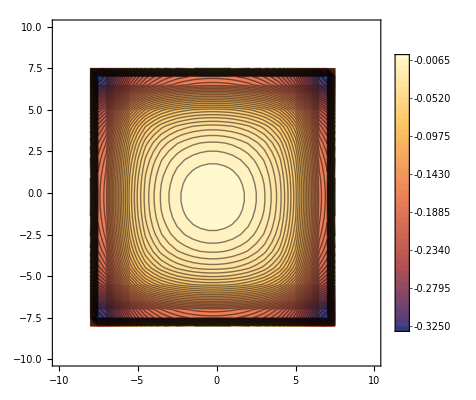
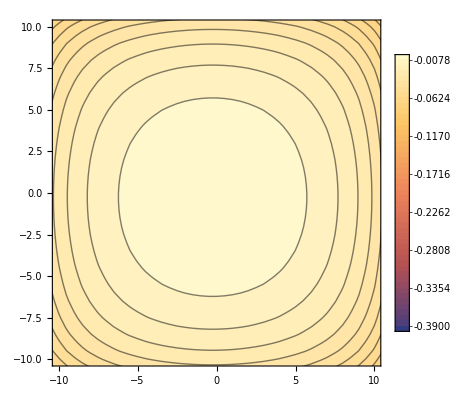
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListContourPlot[values[sols[k]], Contours->50,PlotLegends->Automatic,PlotRange->{{-W,W},{-W,W}}],{k,Keys[sols]}]
```

```mathematica
Clear[slice]
slice[sol_,x2_?NumericQ,y2_?NumericQ]:=Module[{vals,grid,n,i2,j2, fs},
grid=sol["grid"];fs=sol["f"];
(*Find nearest grid indices*)
i2=Nearest[grid->"Index",x2][[1]];
j2=Nearest[grid->"Index",y2][[1]];
vals=Flatten[Table[{grid[[i]],grid[[j]],fs[[i,j,i2,j2]]},{i,sol["n"]},{j,sol["n"]}],1];
vals[[;;,3]]=vals[[;;,3]] - Max[vals[[;;,3]]];
vals
]
u[r_]:=-1/2 A σ^2 (EulerGamma+Gamma[0,r^2/(2 σ^2)]+Log[r^2/(2 σ^2)])
```

```mathematica
sliceAnalitic=Table[{p[[1]],p[[2]],u[√(p[[1]]^2+p[[2]]^2)]/.{A->1, σ->1}},{p,slice[sols[{128,32.0}],0,0]}];
sliceNumeric=slice[sols[{128,32.0}],0,0];
```

General::munfl: Exp[-1030.93] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1015.04] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-999.4] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
diff={sliceAnalitic[[;;,1]],sliceAnalitic[[;;,2]],sliceAnalitic[[;;,3]]-sliceNumeric[[;;,3]]}ᵀ
```

```mathematica
Plot3D[u[√(x^2+y^2)]/.{A->1, σ->1},{x,-W,W},{y,-W,W}]
```

-Graphics3D-

```mathematica
ListPlot3D[diff,PlotRange->{{-W,W},{-W,W}, All},PlotLabel->"f(r, 0)"]
```

-Graphics3D-

```mathematica
ListPlot3D[{sliceAnalitic-sliceNumeric},PlotRange->{{-W,W},{-W,W}, All},PlotLabel->"f(r, 0)"]
```

-Graphics3D-

```mathematica
Show[
ListPlot3D[slice[sols[{128,32.0}],0,0],PlotRange->{{-W,W},{-W,W}, All},PlotLabel->"f(r, 0)"],
Plot3D[u[√(x^2+y^2)]/.{A->1, σ->1},{x,-W,W},{y,-W,W}]
]
```

-Graphics3D-

```mathematica
Manipulate[
ListPlot3D[slice[sols[{128,32.0}],x0,y0],PlotRange->{{-W,W},{-W,W}, All},PlotLabel->"f(r, 0)"],
{{x0,0},-W,W},{{y0,0},-W,W}]
```